# MAD-X TFS file reader

## Function Definitions

```mathematica
madFile[file_]:=Module[
{d,h,dPos,cols},
d=Import[file,"Table"];
h=Cases[d,{"@",___}|{"*",___}|{"$",___}];
d=Cases[d,Except[{"@",___}|{"*",___}|{"$",___}]];
cols=Rest@First@Cases[h,{"*",___}];
d=Thread[Rule@@{cols,Transpose@d}];
{h,d} (*extracts headings and data from a mad file*)
];
madFileToDataset::usage="Takes a mad optics file and returns {header, data}, where data is a Dataset with the columns specified as in the mad file.";
madFileToDataset[file_]:=Module[
{header,data,assocs,keys},
{header,data}=madFile[file];
keys=Keys[data];
assocs=Association[Thread[Rule[keys,#]]]&/@Transpose[keys/.data];
{header,Dataset[assocs]}
];

getTwissAtElement::usage="Takes a string and a data set and returns the list {\"BETX\",\"ALFX\",\"MUX\",\"BETY\",\"ALFY\",\"MUY\"} for the specified element.";
getTwissAtElement[element_String,opticsSet_Dataset]:=Module[
{entry,twiss},
entry=opticsSet[Select[StringMatchQ[element,#NAME]&]];
entry=First[Normal[entry]];
twiss=entry[[Key[#]]]&/@{"BETX","ALFX","MUX","BETY","ALFY","MUY"};
twiss
];

getSAtElement::usage="Takes a string and a data set and returns the s value for the specified element.";
getSAtElement[element_String,opticsSet_Dataset]:=Module[
{entry,s},
entry=opticsSet[Select[StringMatchQ[element,#NAME]&]];
entry=First[Normal[entry]];
s=entry[[Key["S"]]];
s
];

variancesSub:: usage="finds the variance of a single-variable weighted data list from a file";
variancesSub[file_]:=Module[
{x,w,tabX},
tabX=Import[file,"Table"];
{x,w}=Drop[Transpose[tabX],1];
Variance @ WeightedData[x,w]
]

variances:: usage="calculates x, y, and xy variances from input data lists and outputs them in a list of three";
variances[num_Integer,xData_List,yData_List,dData_List]:=Module[ 
{numb,sigx,sigy,sigd,vars},
numb=num;
sigx=variancesSub@xData[[numb]];
sigy=variancesSub@yData[[numb]];
sigd=variancesSub@dData[[numb]];
sigd=sigd-0.5*(sigx+sigy);
vars={sigx,sigy,sigd}
];

covar4x4Calc::usage="fills a 4x4 covariance matrix with data from an 6xN data table";
covar4x4Calc[tab_]:=Module[
{correlationData, numLines, averages, empty},
correlationData=Drop[Transpose[tab],-2];
numLines=Length@correlationData[[1]];
averages={Mean[correlationData[[1]]],Mean[correlationData[[2]]],Mean[correlationData[[3]]],Mean[correlationData[[4]]]};
(*order: x, xp, y, yp*)
empty={{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}};
Module[{i,j,k},
For[j=1,j≤4,j++,
For[k=1,k≤4,k++,
empty[[k,j]]=(1/numLines)*∑_(i=1)^numLines ((correlationData[[k,i]]-averages[[k]])(correlationData[[j,i]]-averages[[j]]));
];];];
empty
];

covarToCorr::usage="constructs a 4x4 correlation matrix from a 4x4 covariance matrix, with 1 all along the diagonal";
covarToCorr[mat_]:=Module[
{sigX,sigXP,sigY,sigYP, sigList,mat2},
sigX=(mat[[1,1]])^(1/2);
sigXP=(mat[[2,2]])^(1/2);
sigY=(mat[[3,3]])^(1/2);
sigYP=(mat[[4,4]])^(1/2);
sigList={sigX,sigXP,sigY,sigYP};
mat2=Table[
mat[[m,n]]/(sigList[[m]]*sigList[[n]])
,{m,1,4}
,{n,1,4}
];
mat2 
];
```

## Definitions

```mathematica
(* 10x, 10y, step=.01 from -.275 *)

startPos="SURV$START"; (****INPUT NEEDED****) (*reconstruction point, s0, string*)
endPos ={"WS02","WS20","WS21","WS23","WS24"}; (****INPUT NEEDED****) (* which wire scanners to use *)(*wire scanner location LIST of strings*)
fileLists={                           (* specify folder(s) *)
Flatten[FileNames[FileNameJoin[{FileNameJoin[{NotebookDirectory[],"*_optics_*"}],"BeamInfo.mu.txt"}]]]};
fileLists=fileLists[[1]];

somwsFile=fileLists[[1]] ;(*contains BET, ALF, MU data*) (****INPUT NEEDED****) (* which optics to use *)
{somwsDataHeader,somwsDataSet}=madFileToDataset[somwsFile];

moswsEndPos =endPos[[2]]; (****INPUT NEEDED****) (*ONE wire scanner location, string*)

comboList=Transpose[madFileToDataset[fileLists[[#]]]&/@Range[5,Length@fileLists,5]]; (* SIM VARIANT *)
{comboDataHeaders,comboDataSets}=comboList;
```

## Twiss Parameters Example

```mathematica
fileLists={
FileNameJoin[{NotebookDirectory[],"optics-test-1"}],
FileNameJoin[{NotebookDirectory[],"optics-test-2"}]
};

{header,dataSet}=madFileToDataset[fileLists[[1]]];
dataSet (*Comment/uncomment to hide/view the data set.*)
getTwissAtElement["QTV_C11",dataSet]

(*Applying to a list of fileLists.*)

{#,getTwissAtElement["QTV_C11",Last@madFileToDataset[#]]}&/@fileLists;
```

Dataset[<>]

{14.5012,0.573589,0.177203,15.5281,0.505342,0.142294}

```mathematica
TwissPos1=getTwissAtElement["Q25",dataSet] (*first location*)
TwissPos2=getTwissAtElement["MARK",dataSet] (*second location*)
```

{6.2227,-0.630381,2.83076,17.0843,1.66486,3.01741}

{68.9826,1.07345,3.39659,7.05838,-0.183575,3.40026}

## R Transform Matrix (RTM) Definition

```mathematica
ClearAll[rTransformMatrix];
rTransformMatrix[{βx1_,αx1_,μx1uncor_,βy1_,αy1_,μy1uncor_},{βx2_,αx2_,μx2uncor_,βy2_,αy2_,μy2uncor_}]:=Module[{μx2=μx2uncor*2*π,μx1=μx1uncor*2*π,μy2=μy2uncor*2*π,μy1=μy1uncor*2*π},{{√(βx2/βx1)(Cos[μx2-μx1]+αx1*Sin[μx2-μx1]),√(βx2*βx1)Sin[μx2-μx1],0,0},
{(-(1+αx2*αx1))/(√(βx2*βx1))Sin[μx2-μx1]+(αx1-αx2)/(√(βx2*βx1))Cos[μx2-μx1],√(βx1/βx2)(Cos[μx2-μx1]-αx2*Sin[μx2-μx1]),0,0},
{0,0,√(βy2/βy1)(Cos[μy2-μy1]+αy1*Sin[μy2-μy1]),√(βy2*βy1)Sin[μy2-μy1]},
{0,0,(-(1+αy2*αy1))/(√(βy2*βy1))Sin[μy2-μy1]+(αy1-αy2)/(√(βy2*βy1))Cos[μy2-μy1],√(βy1/βy2)(Cos[μy2-μy1]-αy2*Sin[μy2-μy1])}}]
```

Test R Matrix

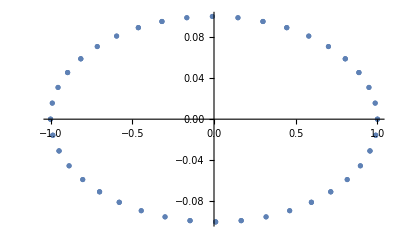
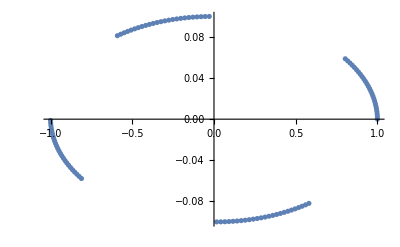

```mathematica
Module[
{test,tracked},
test=rTransformMatrix[{10,0.01,0,10,0.01,0},{10,0.01,0.225,10,0.01,0.249}];
tracked=NestList[test.#&,{1,0,1,0},100];
{ListPlot[tracked[[;;,{1,2}]]],ListPlot[tracked[[;;,{3,4}]]]}
]
```

## Calculate R - Single Optics, Multiple WS (SOMWS)

```mathematica
somwsStartTwiss=getTwissAtElement[startPos,somwsDataSet]; (*get twiss at start*)
somwsEndTwiss1=getTwissAtElement[endPos[[1]],somwsDataSet]; (*get twiss at one endpoint*)
somwsEndTwiss2=getTwissAtElement[endPos[[2]],somwsDataSet]; (*get twiss at one endpoint*)
somwsEndTwiss3=getTwissAtElement[endPos[[3]],somwsDataSet]; (*get twiss at one endpoint*)
somwsEndTwiss4=getTwissAtElement[endPos[[4]],somwsDataSet]; (*get twiss at one endpoint*)
somwsEndTwiss5=getTwissAtElement[endPos[[5]],somwsDataSet]; (*get twiss at one endpoint*)

somwsR1=rTransformMatrix[somwsStartTwiss,somwsEndTwiss1];(*calculate RTM*)
somwsR2=rTransformMatrix[somwsStartTwiss,somwsEndTwiss2];(*calculate RTM*)
somwsR3=rTransformMatrix[somwsStartTwiss,somwsEndTwiss3];(*calculate RTM*)
somwsR4=rTransformMatrix[somwsStartTwiss,somwsEndTwiss4]; (*calculate RTM*)
somwsR5=rTransformMatrix[somwsStartTwiss,somwsEndTwiss5]; (*calculate RTM*)
somwsRs={somwsR1, somwsR2,somwsR3, somwsR4,somwsR5};
MatrixForm/@somwsRs
```

{(-0.632229 | 3.80004 | 0 | 0
-0.385097 | 0.732941 | 0 | 0
0 | 0 | 2.78656 | 6.10843
0 | 0 | 0.423158 | 1.28647),(-3.22624 | 8.92993 | 0 | 0
1.39983 | -4.18456 | 0 | 0
0 | 0 | -5.4254 | -13.4608
0 | 0 | -0.534347 | -1.51007),(2.0025 | -7.33236 | 0 | 0
0.981937 | -3.09609 | 0 | 0
0 | 0 | -2.97424 | -8.13112
0 | 0 | 0.756353 | 1.73154),(10.4298 | -31.3023 | 0 | 0
1.21024 | -3.53633 | 0 | 0
0 | 0 | 1.88726 | 2.99383
0 | 0 | 0.237387 | 0.906447),(5.50935 | -16.089 | 0 | 0
-1.33068 | 4.06751 | 0 | 0
0 | 0 | 5.48555 | 12.3175
0 | 0 | 0.71856 | 1.79578)}

## Calculate R - Multiple Optics, Single WS (MOSWS)

```mathematica
(*apply to full list of fileLists*)
moswsStartTwiss=getTwissAtElement[startPos,Last@madFileToDataset[#]]&/@fileLists;(*get twiss at start, list of 6-item lists*)
moswsEndTwiss=getTwissAtElement[moswsEndPos,Last@madFileToDataset[#]]&/@fileLists; (*get twiss at end, list of 6-item lists*)

moswsRs=Table[
rTransformMatrix[moswsStartTwiss[[j]],moswsEndTwiss[[j]]],(*calculate RTM*)
{j,1,Length@moswsEndTwiss}
];
ClearAll[j];
MatrixForm/@moswsRs
```

{(-3.22624 | 8.92993 | 0 | 0
1.39983 | -4.18456 | 0 | 0
0 | 0 | -5.4254 | -13.4608
0 | 0 | -0.534347 | -1.51007),(-3.10121 | 8.50111 | 0 | 0
1.34145 | -3.99967 | 0 | 0
0 | 0 | 6.75243 | 19.0668
0 | 0 | 0.599258 | 1.84022),(-3.02509 | 8.207 | 0 | 0
1.40131 | -4.13229 | 0 | 0
0 | 0 | -3.60717 | -10.0144
0 | 0 | -0.381691 | -1.3369),(-2.93839 | 7.88308 | 0 | 0
1.4344 | -4.18851 | 0 | 0
0 | 0 | -3.46715 | -7.58331
0 | 0 | -0.557655 | -1.50812),(-2.8207 | 7.4753 | 0 | 0
1.43628 | -4.16088 | 0 | 0
0 | 0 | 2.33717 | 1.73431
0 | 0 | 0.426914 | 0.744661),(-2.29424 | 5.99831 | 0 | 0
1.11573 | -3.35295 | 0 | 0
0 | 0 | -3.64821 | -14.4421
0 | 0 | -0.193317 | -1.03939),(-1.97465 | 5.08488 | 0 | 0
0.648754 | -2.17701 | 0 | 0
0 | 0 | -2.76278 | -10.2108
0 | 0 | -0.0436857 | -0.523411),(-1.85971 | 4.70661 | 0 | 0
1.42403 | -4.1417 | 0 | 0
0 | 0 | -2.26887 | -10.3421
0 | 0 | -0.0499438 | -0.668404),(-1.87274 | 4.64521 | 0 | 0
1.34679 | -3.8746 | 0 | 0
0 | 0 | -3.36704 | -9.21531
0 | 0 | -0.367434 | -1.30263),(-0.131413 | -0.729485 | 0 | 0
0.917834 | -2.51462 | 0 | 0
0 | 0 | 0.837457 | 7.84999
0 | 0 | -0.093575 | 0.316956),(2.5478 | -8.0533 | 0 | 0
-0.309387 | 1.37043 | 0 | 0
0 | 0 | -2.23404 | -4.70864
0 | 0 | -0.495602 | -1.49219),(2.33618 | -7.49498 | 0 | 0
-0.044878 | 0.572028 | 0 | 0
0 | 0 | -5.28885 | -11.6817
0 | 0 | -0.688398 | -1.70957),(1.62605 | -5.66794 | 0 | 0
0.473509 | -1.03553 | 0 | 0
0 | 0 | -2.54873 | -5.8539
0 | 0 | -0.446443 | -1.41774),(2.44058 | -7.58194 | 0 | 0
0.0902364 | 0.129409 | 0 | 0
0 | 0 | -2.7558 | -6.54429
0 | 0 | -0.389413 | -1.28763),(2.62018 | -8.23898 | 0 | 0
-0.0380116 | 0.501178 | 0 | 0
0 | 0 | -2.8997 | -7.08911
0 | 0 | -0.507615 | -1.58587),(2.3868 | -7.41173 | 0 | 0
0.519368 | -1.19383 | 0 | 0
0 | 0 | -3.7564 | -9.42296
0 | 0 | -0.445056 | -1.38264),(-1.96663 | 4.75659 | 0 | 0
1.20555 | -3.42428 | 0 | 0
0 | 0 | -4.81947 | -12.3726
0 | 0 | -0.613025 | -1.78126),(2.15724 | -6.83479 | 0 | 0
0.673538 | -1.67042 | 0 | 0
0 | 0 | -5.6391 | -14.7851
0 | 0 | -0.628922 | -1.82629),(2.46373 | -7.52086 | 0 | 0
0.444823 | -0.951994 | 0 | 0
0 | 0 | -3.71629 | -9.93469
0 | 0 | -0.427299 | -1.41137),(2.39208 | -7.44963 | 0 | 0
0.472804 | -1.0544 | 0 | 0
0 | 0 | -3.40266 | -9.26232
0 | 0 | -0.400176 | -1.3832)}

## Calculate R - Combination SOMWS and MOSWS (COMBO)

```mathematica
(*apply to full list of fileLists*)
comboStartTwiss=getTwissAtElement[startPos,#]&/@comboDataSets; (*get twiss at start, N-item list of 6-item lists*)
(*comboEndTwiss={getTwissAtElement[endPos[[1]],#]&/@comboDataSets,
getTwissAtElement[endPos[[2]],#]&/@comboDataSets,
getTwissAtElement[endPos[[3]],#]&/@comboDataSets,
getTwissAtElement[endPos[[4]],#]&/@comboDataSets,
getTwissAtElement[endPos[[5]],#]&/@comboDataSets};(*get twiss at end. 5-item list of N-item lists of 6-item lists*) 

comboEndTwiss2=Transpose[comboEndTwiss,{2,1,3}] (*sort by optics, then position, then twiss*)*)

comboEndTwiss=Table[   (* sorted by optics, then position, then twiss *)
getTwissAtElement[endPos[[i]],comboDataSets[[j]]],
{j,1,Length@comboDataSets},
{i,1,5}
];(* N-item list of 5-item lists of 6-item lists *)

comboRs=Table[
rTransformMatrix[comboStartTwiss[[j]],comboEndTwiss[[j,k]] ],(*calculate RTM*)
{k,1,Length@endPos}, (* for all wire scanners *)
{j,1,Length@comboEndTwiss} (* for all optics *)
];
ClearAll[j,k];

comboRs=Flatten[comboRs,1]; 
MatrixForm/@comboRs;
Length@comboRs;
```

## Build Measurement Matrix

```mathematica
(****INPUT NEEDED****)(*what measurements?*)

(*moswsRs={};*) (*<-- uncomment to test with empty set*)
(*listOfRs=somwsRs;*)
(*listOfRs=moswsRs;*)
(*listOfRs=Join[somwsRs, moswsRs];*)
listOfRs=comboRs;

ClearAll[r,σ,orderedSigmaElements,generalMeasurementMatrix]
{orderedSigmaElements,generalMeasurementMatrix}=Module[
{
rmat=Table[r[i,j],{i,1,4},{j,1,4}],
σmat=Table[σ[Min[i,j],Max[i,j]],{i,1,4},{j,1,4}],
unknowns,
trans,coefficients,dummy=Array[0&,{10,3}]
},
trans=(rmat.σmat.Transpose[rmat])[[Sequence@@#]]&/@{{1,1},{3,3},{1,3}};(*Take elements xx,yy,xy from σ'*)
unknowns=DeleteDuplicates[Flatten[σmat]];(*This is how our unknown column vector will be ordered, so we'll save it at the end.*)
coefficients=Table[{#,Coefficient[trans[[i]],#,1]}&/@unknowns,{i,1,Length@trans}];(*We extract the coeffecients in terms of r for each element of σ, each unknown.*)
{unknowns,Table[coefficients[[i,j,2]],{i,1,Length@trans},{j,1,Length@unknowns}]}
];

(*We can set the coupling elements to 0.*)
uncoupledMeasurementMatrix=generalMeasurementMatrix/.{r[1,3]->0,r[1,4]->0,r[2,3]->0,r[2,4]->0,r[3,1]->0,r[3,2]->0,r[4,2]->0,r[4,1]->0};

(*
Using the notation r[scanIndex][plane index,σ index] we can give the full uncoupled measurement matrix in general form. From here solving the problem is just a matter of taking the least squares where the answer will be returned as {...10 numbers...}. 
*)

fullUncoupledMeasurementMatrix=Join@@Table[
uncoupledMeasurementMatrix/.Flatten[Table[r[i,j]->r[scanIndex][i,j],{i,1,4},{j,1,4}]],
{scanIndex,1,Length@listOfRs}
];
MatrixForm@fullUncoupledMeasurementMatrix;
For[ (* define all r terms in meas matrix *)
i=1,i≤Length@listOfRs,i++,
rules={r[i][1,1]->listOfRs[[i]][[1,1]],r[i][1,2]->listOfRs[[i]][[1,2]],
r[i][2,1]->listOfRs[[i]][[2,1]],r[i][2,2]->listOfRs[[i]][[2,2]],
r[i][3,3]->listOfRs[[i]][[3,3]],r[i][3,4]->listOfRs[[i]][[3,4]],
r[i][4,3]->listOfRs[[i]][[4,3]],r[i][4,4]->listOfRs[[i]][[4,4]]};
fullUncoupledMeasurementMatrix=fullUncoupledMeasurementMatrix/.rules;
];
ClearAll[i];

MatrixForm@fullUncoupledMeasurementMatrix;
```

## Sigma Matrix Reconstruction

Wire Scanner Measurements

```mathematica
dataWSX=FileNames[FileNameJoin[{NotebookDirectory[],"*_optics_*/ws_*_x.dat"}]]; (* specify folder(s) *)
dataWSY=FileNames[FileNameJoin[{NotebookDirectory[],"*_optics_*/ws_*_y.dat"}]];
dataWSD=FileNames[FileNameJoin[{NotebookDirectory[],"*_optics_*/ws_*_d.dat"}]];
length=Length@dataWSX;(* number of optics * number of WS locations *)

(*wsVars["00"]=variances[#, dataWSX,dataWSY,dataWSD]&/@Range[1,Length@dataWSY,6];*)      (*at WS00 only*)
wsVars["02"]=variances[#, dataWSX,dataWSY,dataWSD]&/@Range[2,length,6];      (*at WS02 only*)
wsVars["20"]=variances[#, dataWSX,dataWSY,dataWSD]&/@Range[3,length,6];      (*at WS20 only*)
wsVars["21"]=variances[#, dataWSX,dataWSY,dataWSD]&/@Range[4,length,6];      (*at WS21 only*)
wsVars["23"]=variances[#, dataWSX,dataWSY,dataWSD]&/@Range[5,length,6];      (*at WS23 only*)
wsVars["24"]=variances[#, dataWSX,dataWSY,dataWSD]&/@Range[6,length,6];      (*at WS24 only*)
wsVars["02"]=wsVars["02"][[5;;20;; 5]]; (* SIM VARIANT *)
wsVars["20"]=wsVars["20"][[5;;20;; 5]];
wsVars["21"]=wsVars["21"][[5;;20;; 5]];
wsVars["23"]=wsVars["23"][[5;;20;; 5 ]];
wsVars["24"]=wsVars["24"][[5;;20;; 5]];

measurements=Flatten[{wsVars["02"],wsVars["20"],wsVars["21"],wsVars["23"],wsVars["24"]}] ;(* *10^-6*) 
Length@measurements
```

60

Visualization of Least Squares Formula

```mathematica
fullEq=Row[{
measurements//MatrixForm
(*=MatrixForm[List/@Join@@Table[{"σ_xx"[i],"σ_yy"[i],"σ_xy"[i]},{i,1,Length@listOfRs}]] *)," = ",
(MatrixForm@fullUncoupledMeasurementMatrix).MatrixForm[List/@orderedSigmaElements]
}]
```

(59.7793
56.2149
-0.709287
59.7793
56.2149
-0.709287
59.7793
56.2149
-0.709287
59.7793
56.2149
-0.709287
50.8442
190.988
-3.49213
23.58
174.253
-5.50004
12.9175
42.3261
-0.0732806
10.9233
40.8217
1.38027
22.2425
68.6712
4.48447
47.9327
63.7662
-10.6691
131.54
18.4101
0.800845
227.523
15.2218
3.54846
342.357
19.5948
-11.1899
234.189
18.6146
4.33037
161.92
43.1343
-8.94732
244.088
51.4195
-0.19709
109.147
171.277
-10.9383
59.9887
155.635
1.1295
23.3059
69.1016
-4.67597
23.1442
80.5715
-0.711053) = (0.399714 | -4.805 | 0 | 0 | 14.4403 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 7.76494 | 34.0431 | 37.313
0 | 0 | -1.76175 | -3.86193 | 0 | 10.5891 | 23.2123 | 0 | 0 | 0
0.399714 | -4.805 | 0 | 0 | 14.4403 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 7.76494 | 34.0431 | 37.313
0 | 0 | -1.76175 | -3.86193 | 0 | 10.5891 | 23.2123 | 0 | 0 | 0
0.399714 | -4.805 | 0 | 0 | 14.4403 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 7.76494 | 34.0431 | 37.313
0 | 0 | -1.76175 | -3.86193 | 0 | 10.5891 | 23.2123 | 0 | 0 | 0
0.399714 | -4.805 | 0 | 0 | 14.4403 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 7.76494 | 34.0431 | 37.313
0 | 0 | -1.76175 | -3.86193 | 0 | 10.5891 | 23.2123 | 0 | 0 | 0
7.95637 | -42.1713 | 0 | 0 | 55.8802 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 5.46238 | 8.10675 | 3.00782
0 | 0 | -6.59247 | -4.89197 | 0 | 17.4711 | 12.9645 | 0 | 0 | 0
0.0172693 | 0.191727 | 0 | 0 | 0.532148 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.701335 | 13.1481 | 61.6224
0 | 0 | -0.110053 | -1.03159 | 0 | -0.610912 | -5.72645 | 0 | 0 | 0
6.86534 | -43.1752 | 0 | 0 | 67.8808 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 8.40826 | 41.1126 | 50.2554
0 | 0 | -7.59773 | -18.5747 | 0 | 23.8906 | 58.407 | 0 | 0 | 0
5.72206 | -35.6403 | 0 | 0 | 55.4971 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 11.5781 | 63.033 | 85.7905
0 | 0 | -8.13944 | -22.1562 | 0 | 25.3485 | 69.0009 | 0 | 0 | 0
8.8635 | -59.1675 | 0 | 0 | 98.7418 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 4.34181 | 13.717 | 10.8339
0 | 0 | 6.20352 | 9.79932 | 0 | -20.7055 | -32.7072 | 0 | 0 | 0
25.5204 | -160.583 | 0 | 0 | 252.611 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0670998 | -1.26545 | 5.96634
0 | 0 | -1.30859 | 12.3395 | 0 | 4.11706 | -38.8222 | 0 | 0 | 0
22.2624 | -119.211 | 0 | 0 | 159.587 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 6.22636 | 37.4643 | 56.3561
0 | 0 | -11.7734 | -35.4206 | 0 | 31.5222 | 94.8352 | 0 | 0 | 0
52.3861 | -291.35 | 0 | 0 | 405.093 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 4.53984 | 29.8241 | 48.9817
0 | 0 | -15.4216 | -50.6553 | 0 | 42.8842 | 140.862 | 0 | 0 | 0
116.348 | -676.73 | 0 | 0 | 984.04 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.978637 | 9.2078 | 21.6586
0 | 0 | 10.6706 | 50.199 | 0 | -31.0325 | -145.989 | 0 | 0 | 0
51.605 | -285.491 | 0 | 0 | 394.851 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 3.626 | 26.3158 | 47.747
0 | 0 | -13.6792 | -49.6385 | 0 | 37.8382 | 137.306 | 0 | 0 | 0
0.0247584 | 0.78732 | 0 | 0 | 6.2592 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.05131 | 11.6193 | 32.1045
0 | 0 | -0.161334 | -0.891547 | 0 | -2.56522 | -14.1756 | 0 | 0 | 0
17.0439 | -79.0571 | 0 | 0 | 91.6756 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.345397 | -1.28425 | 1.19377
0 | 0 | 2.42629 | -4.5107 | 0 | -5.62712 | 10.4613 | 0 | 0 | 0
29.0757 | -164.467 | 0 | 0 | 232.577 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.967264 | -4.46646 | 5.15611
0 | 0 | -5.3032 | 12.2441 | 0 | 14.9988 | -34.6294 | 0 | 0 | 0
6.53423 | -32.8389 | 0 | 0 | 41.2595 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 4.33212 | 46.357 | 124.014
0 | 0 | -5.32043 | -28.4664 | 0 | 13.3694 | 71.5314 | 0 | 0 | 0
2.24335 | -17.205 | 0 | 0 | 32.9879 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.89024 | 2.5924 | 0.88885
0 | 0 | -2.05924 | -1.41209 | 0 | 7.89651 | 5.41491 | 0 | 0 | 0
0.0000541176 | 0.0163241 | 0 | 0 | 1.231 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 8.90551 | 36.1825 | 36.7517
0 | 0 | 0.0219532 | 0.0445973 | 0 | 3.31099 | 6.72617 | 0 | 0 | 0).(σ[1,1]
σ[1,2]
σ[1,3]
σ[1,4]
σ[2,2]
σ[2,3]
σ[2,4]
σ[3,3]
σ[3,4]
σ[4,4])

Least Squares Calculation

```mathematica
final=LeastSquares[fullUncoupledMeasurementMatrix[[1;;-1;;2]],measurements[[1;;-1;;2]]];(*reconstruct sigma0 values*)
(*altFinal=Inverse[Transpose[fullUncoupledMeasurementMatrix].fullUncoupledMeasurementMatrix].Transpose[fullUncoupledMeasurementMatrix].measurements20*)
PseudoInverse[fullUncoupledMeasurementMatrix].measurements;
final4D={{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}};
final4D[[1,1]]=final[[1]]; (*assign sigma0 values to 4x4 matrix*)
final4D[[1,2]]=final4D[[2,1]]=final[[2]];
final4D[[1,3]]=final4D[[3,1]]=final[[3]];
final4D[[1,4]]=final4D[[4,1]]=final[[4]];
final4D[[2,2]]=final[[5]];
final4D[[2,3]]=final4D[[3,2]]=final[[6]];
final4D[[2,4]]=final4D[[4,2]]=final[[7]];
final4D[[3,3]]=final[[8]];
final4D[[3,4]]=final4D[[4,3]]=final[[9]];
final4D[[4,4]]=final[[10]];
final4D//MatrixForm

finalCorrelation=covarToCorr[final4D] ;
MatrixForm[finalCorrelation]
```

(180.679 | 56.7624 | -4.81365 | 2.19153
56.7624 | 18.0212 | -2.0857 | 0.922233
-4.81365 | -2.0857 | 58.9645 | -18.4906
2.19153 | 0.922233 | -18.4906 | 6.10536)

(1. | 0.994753 | -0.0466365 | 0.0659839
0.994753 | 1. | -0.0639829 | 0.0879211
-0.0466365 | -0.0639829 | 1. | -0.974541
0.0659839 | 0.0879211 | -0.974541 | 1.)

## Input Distribution Check

Input Covariance & Comparison

```mathematica
rawData=(****INPUT NEEDED****)(*need file name/location*)Import["/Users/4tc/Dropbox/suli 2018 project/y_optics_0001/initial.mu.txt","Table"];
rawData=Cases[rawData,Except[{"%",___}]]; (* for initial and final bunch dumps *)

covar=covar4x4Calc[rawData]*10^6;
corr=covarToCorr[covar];
corr2=covarToCorr[final4D];
"covariance from input distribution:"  MatrixForm[covar]
"covariance from Least Squares:"  MatrixForm[final4D]
"correlation from input distribution:" MatrixForm[corr]
"correlation from Least Squares:" MatrixForm[corr2]
```

covariance from input distribution: (174.925 | 54.9352 | -4.6319 | 2.09627
54.9352 | 17.4312 | -2.00851 | 0.884497
-4.6319 | -2.00851 | 56.8924 | -17.8275
2.09627 | 0.884497 | -17.8275 | 5.88035)

covariance from Least Squares: (180.679 | 56.7624 | -4.81365 | 2.19153
56.7624 | 18.0212 | -2.0857 | 0.922233
-4.81365 | -2.0857 | 58.9645 | -18.4906
2.19153 | 0.922233 | -18.4906 | 6.10536)

correlation from input distribution: (1. | 0.994855 | -0.0464308 | 0.0653612
0.994855 | 1. | -0.0637796 | 0.0873636
-0.0464308 | -0.0637796 | 1. | -0.974681
0.0653612 | 0.0873636 | -0.974681 | 1.)

correlation from Least Squares: (1. | 0.994753 | -0.0466365 | 0.0659839
0.994753 | 1. | -0.0639829 | 0.0879211
-0.0466365 | -0.0639829 | 1. | -0.974541
0.0659839 | 0.0879211 | -0.974541 | 1.)

```mathematica
listedCovar1={covar[[1,1]],covar[[1,2]],covar[[1,3]],covar[[1,4]],covar[[2,2]],covar[[2,3]],covar[[2,4]],covar[[3,3]],covar[[3,4]],covar[[4,4]]};
listedCovar2={final4D[[1,1]],final4D[[1,2]],final4D[[1,3]],final4D[[1,4]],final4D[[2,2]],final4D[[2,3]],final4D[[2,4]],final4D[[3,3]],final4D[[3,4]],final4D[[4,4]]};
listedCorr1={corr[[1,2]],corr[[1,3]],corr[[1,4]],corr[[2,3]],corr[[2,4]],corr[[3,4]]};
listedCorr2={corr2[[1,2]],corr2[[1,3]],corr2[[1,4]],corr2[[2,3]],corr2[[2,4]],corr2[[3,4]]};

ListPlot[
{listedCovar1,listedCovar2}-> {{"xx","xx'","xy","xy'","x'x'","x'y","x'y'","yy","yy'","y'y'"},None},(*LabelingFunction->Callout[Automatic],*)
Joined->{False, True}, PlotRange->All, ImageSize->Large,
Frame->True, FrameLabel->{"Position","Covariance"}, GridLines->Automatic]
ListPlot[
{listedCorr1,listedCorr2}-> {{"xx'","xy","xy'","x'y","x'y'","yy'"},None},
(*LabelingFunction->Callout[Automatic],*)
Joined->{False, True}, PlotRange->All, ImageSize->Large,
Frame->True, FrameLabel->{"Position","Correlation"}, GridLines->Automatic]
```

-Graphics-

-Graphics-

## Phase Shift Investigation (x)

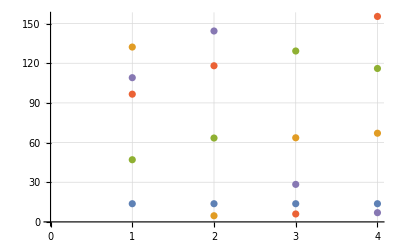

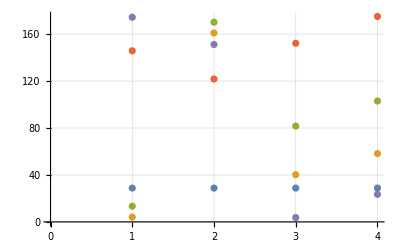

```mathematica
(*phaseShift0220=Transpose[comboEndTwiss,{1,3,2}][[1,6]]-comboStartTwiss[[1,6]];*)
comboEndTwiss2=Transpose[comboEndTwiss,{2,1,3}] ;
phaseShiftX=comboEndTwiss2[[;;,;;,3]]-comboStartTwiss[[1,3]];
phaseShiftY=comboEndTwiss2[[;;,;;,6]]-comboStartTwiss[[1,6]];
(*pointList=Transpose[{Range[Length@phaseShift0220],phaseShift0220}];*)
(*ListPlot[Drop[pointList,-3]]*)
ListPlot[
Mod[phaseShiftX*360,180]
,GridLines->Automatic]

ListPlot[
Mod[phaseShiftY*360,180]
,GridLines->Automatic]
```

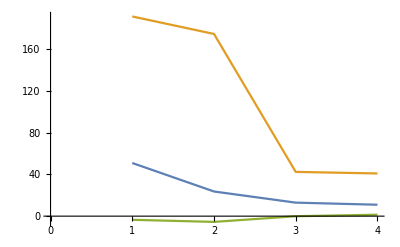

```mathematica
(*ListPlot[measurements02]*)
ListPlot[
Transpose[wsVars["20"]]
, PlotRange->All
,AxesOrigin->{0,0}
,Joined->True
]
```

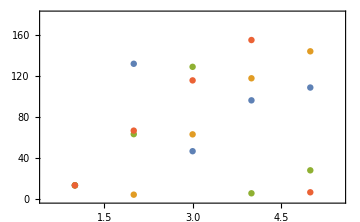

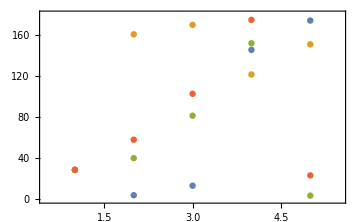

```mathematica
ListPlot[
Mod[Transpose@phaseShiftX*360,180],
PlotRange->{{.5,5.5},{0,180}},
Frame->True, ImageSize->Medium
]
ListPlot[
Mod[Transpose@phaseShiftY*360,180],
PlotRange->{{0.5,5.5},{0,180}},
Frame->True, ImageSize->Medium
]
```

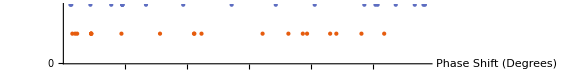

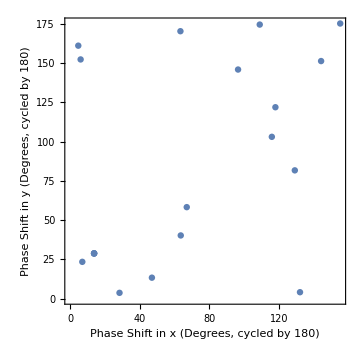

```mathematica
(*NumberLinePlot[Flatten[Mod[phaseShiftX*360,180]]]
NumberLinePlot[Flatten[Mod[phaseShiftY*360,180]]]
NumberLinePlot[Interval[{0,180}]]*)
NumberLinePlot[{Flatten[Mod[phaseShiftX*360,180]],Flatten[Mod[phaseShiftY*360,180]]},PlotTheme->"DarkColor",ImageSize-> Large,Ticks->{Range[0,180,30]},AxesLabel->{HoldForm["Phase Shift (Degrees)"],None}, PlotLegends->Placed[{"x","y"},Left]]

ListPlot[
Transpose@{
Flatten[Mod[phaseShiftX*360,180]],
Flatten[Mod[phaseShiftY*360,180]]
},
AspectRatio->1,ImageSize->Medium,
Frame->True, FrameLabel->{"Phase Shift in x (Degrees, cycled by 180)","Phase Shift in y (Degrees, cycled by 180)"}
]
```

## Twiss Plotter

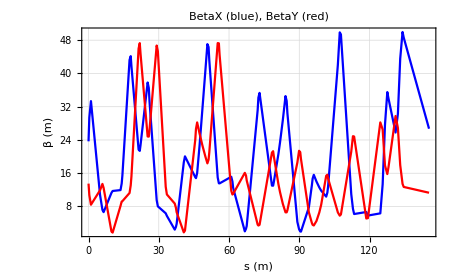

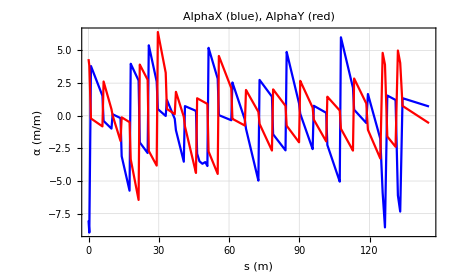

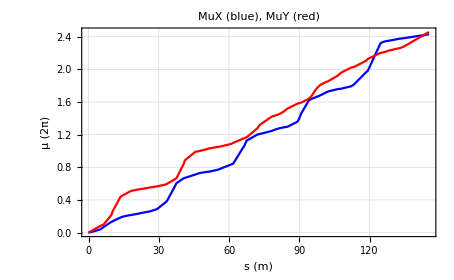

```mathematica
(* choose optics set *)
whichOptics=1;
elements=Normal[comboDataSets[[whichOptics]][[All,"NAME"]]];
twiss=getTwissAtElement[elements[[#]],comboDataSets[[whichOptics]]]&/@Range[Length@elements];

betaX=twiss[[#,1]] &/@ Range[Length@elements];
alphaX=twiss[[#,2]] &/@ Range[Length@elements];
muX=twiss[[#,3]] &/@ Range[Length@elements];
betaY=twiss[[#,4]] &/@ Range[Length@elements];
alphaY=twiss[[#,5]] &/@ Range[Length@elements];
muY=twiss[[#,6]] &/@ Range[Length@elements];
(* 1 through 6 for "BETX","ALFX","MUX","BETY","ALFY","MUY" *)

sVals=getSAtElement[elements[[#]],comboDataSets[[whichOptics]]]&/@Range[Length@elements];
Length@elements;

bx=ListPlot[
{Transpose[{sVals,betaX}]},
PlotStyle->Blue,
Joined->True,
GridLines->Automatic
];
by=ListPlot[
{Transpose[{sVals,betaY}]},
PlotStyle->Red,
Joined->True,
GridLines->Automatic
];
ax=ListPlot[
{Transpose[{sVals,alphaX}]},
PlotStyle->Blue,
Joined->True,
GridLines->Automatic
];
ay=ListPlot[
{Transpose[{sVals,alphaY}]},
PlotStyle->Red,
Joined->True,
GridLines->Automatic
];
mx=ListPlot[ (* left in units of 2pi *)
{Transpose[{sVals,muX}]},
PlotStyle->Blue,
Joined->True,
GridLines->Automatic
];
my=ListPlot[(* left in units of 2pi *)
{Transpose[{sVals,muY}]},
PlotStyle->Red,
Joined->True,
GridLines->Automatic
];
Show[bx,by,PlotRange->All,Frame->True,AxesLabel->None,FrameLabel->{{HoldForm[HoldForm["β (m)"]],None},{HoldForm[HoldForm["s (m)"]],None}},PlotLabel->RawBoxes[RowBox[{RowBox[{"BetaX"," ",RowBox[{"(","blue",")"}]}],","," ",RowBox[{"BetaY"," ",RowBox[{"(","red",")"}]}]}]],LabelStyle->{FontFamily->"Titillium Web",13,GrayLevel[0]}]

Show[ax,ay,PlotRange->All,Frame->True,AxesLabel->None,FrameLabel->{{HoldForm[HoldForm["α (m/m)"]],None},{HoldForm[HoldForm["s (m)"]],None}},PlotLabel->RawBoxes[RowBox[{RowBox[{"AlphaX"," ",RowBox[{"(","blue",")"}]}],","," ",RowBox[{"AlphaY"," ",RowBox[{"(","red",")"}]}]}]],LabelStyle->{FontFamily->"Titillium Web",13,GrayLevel[0]}]

Show[mx,my,PlotRange->All,Frame->True,AxesLabel->None,FrameLabel->{{HoldForm[HoldForm["μ (2π)"]],None},{HoldForm[HoldForm["s (m)"]],None}},PlotLabel->RawBoxes[RowBox[{RowBox[{"MuX"," ",RowBox[{"(","blue",")"}]}],","," ",RowBox[{"MuY"," ",RowBox[{"(","red",")"}]}]}]],LabelStyle->{FontFamily->"Titillium Web",13,GrayLevel[0]}]
```

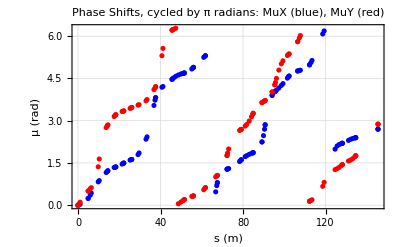

```mathematica
mx2=ListPlot[ (* left in units of 2pi *)
{Transpose[{sVals,Mod[muX*2π,2π]}]},
PlotStyle->Blue,
(*Joined->True,*)
GridLines->Automatic
];
my2=ListPlot[(* left in units of 2pi *)
{Transpose[{sVals,Mod[muY*2π,2π]}]},
PlotStyle->Red,
(*Joined->True,*)
GridLines->Automatic
];
Show[mx2,my2,PlotRange->All,Frame->True,AxesLabel->None,FrameLabel->{{HoldForm[HoldForm["μ (rad)"]],None},{HoldForm[HoldForm["s (m)"]],None}},PlotLabel->"Phase Shifts, cycled by π radians:  MuX (blue),  MuY (red)",LabelStyle->{FontFamily->"Titillium Web",12,GrayLevel[0]}]
```

## Discussion

### Tests:

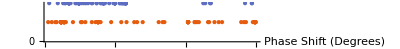

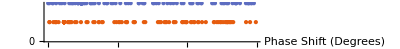

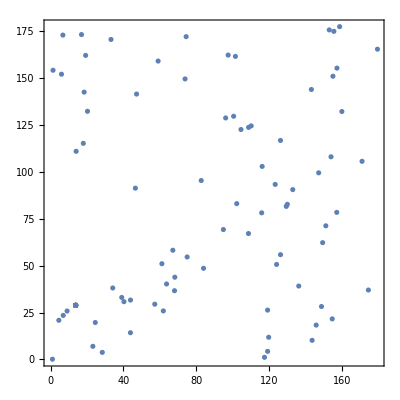

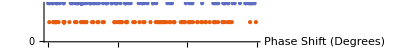

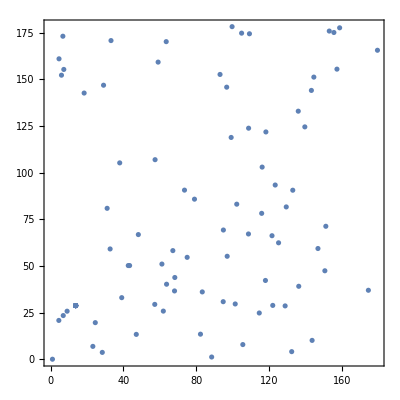

```mathematica
comboDataHeaders;
getSAtElement["WS24", comboDataSets[[1]]]
```

112.191

```mathematica
fileLists
```

{/Users/4tc/Dropbox/suli 2018 project/x_optics_0001/BeamInfo.mu.txt,/Users/4tc/Dropbox/suli 2018 project/x_optics_0002/BeamInfo.mu.txt,/Users/4tc/Dropbox/suli 2018 project/x_optics_0003/BeamInfo.mu.txt,/Users/4tc/Dropbox/suli 2018 project/x_optics_0004/BeamInfo.mu.txt,/Users/4tc/Dropbox/suli 2018 project/x_optics_0005/BeamInfo.mu.txt,/Users/4tc/Dropbox/suli 2018 project/x_optics_0006/BeamInfo.mu.txt,/Users/4tc/Dropbox/suli 2018 project/x_optics_0007/BeamInfo.mu.txt,/Users/4tc/Dropbox/suli 2018 project/x_optics_0008/BeamInfo.mu.txt,/Users/4tc/Dropbox/suli 2018 project/x_optics_0009/BeamInfo.mu.txt,/Users/4tc/Dropbox/suli 2018 project/x_optics_0010/BeamInfo.mu.txt,/Users/4tc/Dropbox/suli 2018 project/y_optics_0001/BeamInfo.mu.txt,/Users/4tc/Dropbox/suli 2018 project/y_optics_0002/BeamInfo.mu.txt,/Users/4tc/Dropbox/suli 2018 project/y_optics_0003/BeamInfo.mu.txt,/Users/4tc/Dropbox/suli 2018 project/y_optics_0004/BeamInfo.mu.txt,/Users/4tc/Dropbox/suli 2018 project/y_optics_0005/BeamInfo.mu.txt,/Users/4tc/Dropbox/suli 2018 project/y_optics_0006/BeamInfo.mu.txt,/Users/4tc/Dropbox/suli 2018 project/y_optics_0007/BeamInfo.mu.txt,/Users/4tc/Dropbox/suli 2018 project/y_optics_0008/BeamInfo.mu.txt,/Users/4tc/Dropbox/suli 2018 project/y_optics_0009/BeamInfo.mu.txt,/Users/4tc/Dropbox/suli 2018 project/y_optics_0010/BeamInfo.mu.txt}

```mathematica
NotebookDirectory[]"x_optics_0001/"
```

/Users/4tc/Dropbox/suli 2018 project/sim1/ x_optics_0001/

```mathematica
Flatten[FileNames[FileNameJoin[{"/Users/4tc/Dropbox/suli 2018 project/sim1/x_optics_0001","BeamInfo.mu.txt"}]]]
```

{/Users/4tc/Dropbox/suli 2018 project/sim1/x_optics_0001/BeamInfo.mu.txt}

```mathematica
Flatten[FileNames[FileNameJoin[{FileNameJoin[NotebookDirectory[]"x_optics_0001"],"BeamInfo.mu.txt"}]]]
```

{}

```mathematica
dir=NotebookDirectory[];
FileNameJoin[{dir,"x_optics_0001"}]
Flatten[FileNames[FileNameJoin[{FileNameJoin[{NotebookDirectory[],"*_optics_*"}],"BeamInfo.mu.txt"}]]]
```

/Users/4tc/Dropbox/suli 2018 project/sim1/x_optics_0001

{/Users/4tc/Dropbox/suli 2018 project/sim1/x_optics_0001/BeamInfo.mu.txt,/Users/4tc/Dropbox/suli 2018 project/sim1/x_optics_0002/BeamInfo.mu.txt,/Users/4tc/Dropbox/suli 2018 project/sim1/x_optics_0003/BeamInfo.mu.txt,/Users/4tc/Dropbox/suli 2018 project/sim1/x_optics_0004/BeamInfo.mu.txt,/Users/4tc/Dropbox/suli 2018 project/sim1/x_optics_0005/BeamInfo.mu.txt,/Users/4tc/Dropbox/suli 2018 project/sim1/x_optics_0006/BeamInfo.mu.txt,/Users/4tc/Dropbox/suli 2018 project/sim1/x_optics_0007/BeamInfo.mu.txt,/Users/4tc/Dropbox/suli 2018 project/sim1/x_optics_0008/BeamInfo.mu.txt,/Users/4tc/Dropbox/suli 2018 project/sim1/x_optics_0009/BeamInfo.mu.txt,/Users/4tc/Dropbox/suli 2018 project/sim1/x_optics_0010/BeamInfo.mu.txt,/Users/4tc/Dropbox/suli 2018 project/sim1/y_optics_0001/BeamInfo.mu.txt,/Users/4tc/Dropbox/suli 2018 project/sim1/y_optics_0002/BeamInfo.mu.txt,/Users/4tc/Dropbox/suli 2018 project/sim1/y_optics_0003/BeamInfo.mu.txt,/Users/4tc/Dropbox/suli 2018 project/sim1/y_optics_0004/BeamInfo.mu.txt,/Users/4tc/Dropbox/suli 2018 project/sim1/y_optics_0005/BeamInfo.mu.txt,/Users/4tc/Dropbox/suli 2018 project/sim1/y_optics_0006/BeamInfo.mu.txt,/Users/4tc/Dropbox/suli 2018 project/sim1/y_optics_0007/BeamInfo.mu.txt,/Users/4tc/Dropbox/suli 2018 project/sim1/y_optics_0008/BeamInfo.mu.txt,/Users/4tc/Dropbox/suli 2018 project/sim1/y_optics_0009/BeamInfo.mu.txt,/Users/4tc/Dropbox/suli 2018 project/sim1/y_optics_0010/BeamInfo.mu.txt}

```mathematica
FileNames[{"~/Dropbox/suli 2018 project/*_optics*/ws_*_x.dat"}] ;
Length@FileNames[FileNameJoin[{NotebookDirectory[],"*_optics_*/ws_*_x.dat"}]]
```

120

```mathematica
Range[Round[(Length@fileLists)/2]]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Range[2,Length@fileLists,2]
```

{2,4,6,8,10,12,14,16,18,20}

```mathematica
listTest=variances[#, dataWSX,dataWSY,dataWSD]&/@Range[2,length,6]
listTest[[2;;20;; 2]]
```

{{59.7793,56.2149,-0.709287},{59.7793,56.2149,-0.709287},{59.7793,56.2149,-0.709287},{59.7793,56.2149,-0.709287},{59.7793,56.2149,-0.709287},{59.7793,56.2149,-0.709287},{59.7793,56.2149,-0.709287},{59.7793,56.2149,-0.709287},{59.7793,56.2149,-0.709287},{59.7793,56.2149,-0.709287},{59.7793,56.2149,-0.709287},{59.7793,56.2149,-0.709287},{59.7793,56.2149,-0.709287},{59.7793,56.2149,-0.709287},{59.7793,56.2149,-0.709287},{59.7793,56.2149,-0.709287},{59.7793,56.2149,-0.709287},{59.7793,56.2149,-0.709287},{59.7793,56.2149,-0.709287},{59.7793,56.2149,-0.709287}}

{{59.7793,56.2149,-0.709287},{59.7793,56.2149,-0.709287},{59.7793,56.2149,-0.709287},{59.7793,56.2149,-0.709287},{59.7793,56.2149,-0.709287},{59.7793,56.2149,-0.709287},{59.7793,56.2149,-0.709287},{59.7793,56.2149,-0.709287},{59.7793,56.2149,-0.709287},{59.7793,56.2149,-0.709287}}